```mathematica
√((0.004/Sqrt[3])^2+0.001^2)
```

0.00251661

```mathematica
(1+2+0+7+7)/5//N
```

3.4

```mathematica
√3
```

```mathematica
average[list_]:=Sum[list[[i]],{i,1,Length[list]}]/Length[list];sigma[list_]:=√(Sum[(list[[i]]-average[list])^2,{i,1,Length[list]}]/(Length[list]*(Length[list]-1)))
```

```mathematica
l={0.111,0.112,0.110,0.117,0.117}
```

{0.111,0.112,0.11,0.117,0.117}

```mathematica
average[l]
```

0.1134

```mathematica
√((sigma[l])^2+0.05^2/3)
```

0.0289066

```mathematica
0.1134/200
```

0.000567

```mathematica
l2={{0,2.925},{200.20,3.05},{400.23,3.16},{600.41,3.255},{800.46,3.365},{1000.39,3.48},{1200.39,3.61},{1400.56,3.71},{1600.68,3.84},{1800.53,3.95}}
```

{{0,2.925},{200.2,3.05},{400.23,3.16},{600.41,3.255},{800.46,3.365},{1000.39,3.48},{1200.39,3.61},{1400.56,3.71},{1600.68,3.84},{1800.53,3.95}}

```mathematica
l2[[2,1]]
```

200.2

```mathematica
LinearModelFit[l2,{x},{x}]
```

FittedModel[2.92484+0.000566046 x]

```mathematica
%12["AdjustedRSquared"]
```

```mathematica
√0.9991413706000194
```

0.999571

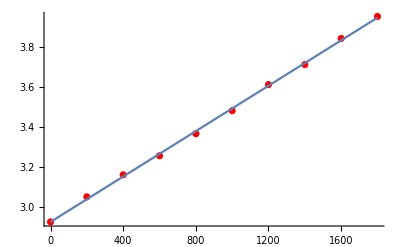

```mathematica
Show[ListPlot[l2,PlotStyle->Red],Plot[%12[x],{x,0,1800.53}]]
```

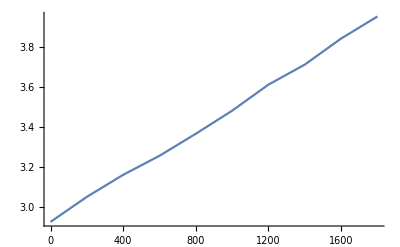

```mathematica
ListPlot[l2,Joined->True]
```

```mathematica
g=9.8012;L=77.15;d=0.324;(4g L)/(π d^2)*1/5.66
```

1620.39

```mathematica
1.61753*√((1.5/(771.5*√3))^2+(2*0.003/0.324)^2+(0.006/0.1134)^2)
```

0.0906924

```mathematica
5.66*10^-4*√((1/0.999570593104869^2-1)/(10-2))
```

5.86625×10^-6

```mathematica
(0.05/√3*1/5)/(√Sum[(l2[[i,1]]-average[l2][[1]])^2,{i,1,10}])
```

3.17728×10^-6

```mathematica
average[l2]
```

{900.385,3.4345}

```mathematica
√(5.86625374182746*^-6^2+3.1772794839398574*^-6^2)
```

6.67143×10^-6

```mathematica
0.03*1/5
```

0.006

```mathematica
1.62039*√((1.5/(771.5*√3))^2+(2*0.003/0.324)^2+((6.671434469630186*^-6)/(5.66*10^-4))^2)
```

0.0356165

```mathematica
E=(g l^3)/(4 a h^3)*m/λ
```